# IPPT Model

## 3d. 2-Set Data Import, Multiple Pulse

Description:
- This notebook will import the results from “3b. Multiple-Pulse Data Export” for any propellant choice using two input files for steady-state data.
- Results are imported from WDX format from desired file path on PC.

How to Run:
- First, evaluate notebooks 1 and 2b for propellant of choice. Export data using 3b to create a WDX file type.
- Pull the desired three files to “Documents” folder on PC, or to whichever folder Mathematica is auto-tethered.
- Either click “Evaluate Notebook” in Menu Options or import file manually.

## Data Import

Notes:
- Adjust the date the files were produced and the shot numbers to reflect desired data sources

```mathematica
Filename1="2022-02-07_v1.12_run_9.wdx";
Filename2="2022-02-13_v1.12_run_11.wdx";

shotdata1 = Import[Filename1];
shotdata2 = Import[Filename2];
```

## Unpack Data

```mathematica
(** Dataset 1 **)
(* ICs *)
zmax1=shotdata1[[1]];
zsteps1=shotdata1[[2]];
tmax1=shotdata1[[3]];
tsteps1=shotdata1[[4]];
zs01=shotdata1[[5]];
ws01=shotdata1[[6]];
χi01=shotdata1[[7]];
zχi1=shotdata1[[8]];
nn01=shotdata1[[9]];
zn1=shotdata1[[10]];
Te01=shotdata1[[11]];
Ti01=shotdata1[[12]];
Lc1=shotdata1[[13]];
L01=shotdata1[[14]];
Rc1=shotdata1[[15]];
C01=shotdata1[[16]];
V01=shotdata1[[17]];
zc1=shotdata1[[18]];
zc01=shotdata1[[19]];
rout1=shotdata1[[20]];
rin1=shotdata1[[21]];
frep1 = shotdata1[[22]];
Np1 =shotdata1[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable1=shotdata2[[24]];
nttable1=shotdata2[[25]];
ntrectable1=shotdata2[[26]];
nmtable1=shotdata2[[27]];
piion1table1=shotdata2[[28]];
piion2table1=shotdata2[[29]];
picextable1=shotdata2[[30]];
(* Pulse 1 state/performance *)
nni1=shotdata1[[31]];
wsi1=shotdata1[[32]];
zsi1=shotdata1[[33]];
vsi1=shotdata1[[34]];
vfi1=shotdata1[[35]];
nsi1=shotdata1[[36]];
nfi1=shotdata1[[37]];
Ici1=shotdata1[[38]];
Ipi1=shotdata1[[39]];
Mi1=shotdata1[[40]];
Vi1=shotdata1[[41]];
Tei1=shotdata1[[42]];
Tii1=shotdata1[[43]];
psi1=shotdata1[[44]];
KEsi1=shotdata1[[45]];
Efi1=shotdata1[[46]];
mbiti1=shotdata1[[47]];
msi1[t_]=shotdata1[[48]];
Epii1=shotdata1[[49]];
Eeli1=shotdata1[[50]];
Eindi1[t_]=shotdata1[[51]];
Ecapi1[t_]=shotdata1[[52]];
Ekei1[t_]=shotdata1[[53]];
EkePli1[t_]=shotdata1[[54]];
EkeEnti1[t_]=shotdata1[[55]];
Etei1[t_]=shotdata1[[56]];
Ibiti1[t_]=shotdata1[[57]];
Ispi1[t_]=shotdata1[[58]];
ηmi1[t_]=shotdata1[[59]];
MassFraci1[t_]=shotdata1[[60]];
ηTi1[t_]=shotdata1[[61]];
ηTreci1[t_]=shotdata1[[62]];
Πioni1[t_]=shotdata1[[63]];
Πion2i1[t_]=shotdata1[[64]];
Πcex2i1[t_]=shotdata1[[65]];
(* Pulse n state/performance *)
nnf1=shotdata1[[66]];
wsf1=shotdata1[[67]];
zsf1=shotdata1[[68]];
vsf1=shotdata1[[69]];
vff1=shotdata1[[70]];
nsf1=shotdata1[[71]];
nff1=shotdata1[[72]];
Icf1=shotdata1[[73]];
Ipf1=shotdata1[[74]];
Mf1=shotdata1[[75]];
Vf1=shotdata1[[76]];
Tef1=shotdata1[[77]];
Tif1=shotdata1[[78]];
psf1=shotdata1[[79]];
KEsf1=shotdata1[[80]];
Eff1=shotdata1[[81]];
mbitf1=shotdata1[[82]];
msf1[t_]=shotdata1[[83]];
Epif1=shotdata1[[84]];
Eelf1=shotdata1[[85]];
Eindf1[t_]=shotdata1[[86]];
Ecapf1[t_]=shotdata1[[87]];
Ekef1[t_]=shotdata1[[88]];
EkePlf1[t_]=shotdata1[[89]];
EkeEntf1[t_]=shotdata1[[90]];
Etef1[t_]=shotdata1[[91]];
Ibitf1[t_]=shotdata1[[92]];
Ispf1[t_]=shotdata1[[93]];
ηmf1[t_]=shotdata1[[94]];
MassFracf1[t_]=shotdata1[[95]];
ηTf1[t_]=shotdata1[[96]];
ηTrecf1[t_]=shotdata1[[97]];
Πionf1[t_]=shotdata1[[98]];
Πion2f1[t_]=shotdata1[[99]];
Πcex2f1[t_]=shotdata1[[100]];

(** Dataset 2 **)
(* ICs *)
zmax2=shotdata2[[1]];
zsteps2=shotdata2[[2]];
tmax2=shotdata2[[3]];
tsteps2=shotdata2[[4]];
zs02=shotdata2[[5]];
ws02=shotdata2[[6]];
χi02=shotdata2[[7]];
zχi2=shotdata2[[8]];
nn02=shotdata2[[9]];
zn2=shotdata2[[10]];
Te02=shotdata2[[11]];
Ti02=shotdata2[[12]];
Lc2=shotdata2[[13]];
L02=shotdata2[[14]];
Rc2=shotdata2[[15]];
C02=shotdata2[[16]];
V02=shotdata2[[17]];
zc2=shotdata2[[18]];
zc02=shotdata2[[19]];
rout2=shotdata2[[20]];
rin2=shotdata2[[21]];
frep2 = shotdata2[[22]];
Np2 =shotdata2[[23]]; 
(* Per-pulse performance metrics and nondimesionalized parameters *)
Isptable2=shotdata2[[24]];
nttable2=shotdata2[[25]];
ntrectable2=shotdata2[[26]];
nmtable2=shotdata2[[27]];
piion1table2=shotdata2[[28]];
piion2table2=shotdata2[[29]];
picextable2=shotdata2[[30]];
(* Pulse 1 state/performance *)
nni2=shotdata2[[31]];
wsi2=shotdata2[[32]];
zsi2=shotdata2[[33]];
vsi2=shotdata2[[34]];
vfi2=shotdata2[[35]];
nsi2=shotdata2[[36]];
nfi2=shotdata2[[37]];
Ici2=shotdata2[[38]];
Ipi2=shotdata2[[39]];
Mi2=shotdata2[[40]];
Vi2=shotdata2[[41]];
Tei2=shotdata2[[42]];
Tii2=shotdata2[[43]];
psi2=shotdata2[[44]];
KEsi2=shotdata2[[45]];
Efi2=shotdata2[[46]];
mbiti2=shotdata2[[47]];
msi2[t_]=shotdata2[[48]];
Epii2=shotdata2[[49]];
Eeli2=shotdata2[[50]];
Eindi2[t_]=shotdata2[[51]];
Ecapi2[t_]=shotdata2[[52]];
Ekei2[t_]=shotdata2[[53]];
EkePli2[t_]=shotdata2[[54]];
EkeEnti2[t_]=shotdata2[[55]];
Etei2[t_]=shotdata2[[56]];
Ibiti2[t_]=shotdata2[[57]];
Ispi2[t_]=shotdata2[[58]];
ηmi2[t_]=shotdata2[[59]];
MassFraci2[t_]=shotdata2[[60]];
ηTi2[t_]=shotdata2[[61]];
ηTreci2[t_]=shotdata2[[62]];
Πioni2[t_]=shotdata2[[63]];
Πion2i2[t_]=shotdata2[[64]];
Πcex2i2[t_]=shotdata2[[65]];
(* Pulse n state/performance *)
nnf2=shotdata2[[66]];
wsf2=shotdata2[[67]];
zsf2=shotdata2[[68]];
vsf2=shotdata2[[69]];
vff2=shotdata2[[70]];
nsf2=shotdata2[[71]];
nff2=shotdata2[[72]];
Icf2=shotdata2[[73]];
Ipf2=shotdata2[[74]];
Mf2=shotdata2[[75]];
Vf2=shotdata2[[76]];
Tef2=shotdata2[[77]];
Tif2=shotdata2[[78]];
psf2=shotdata2[[79]];
KEsf2=shotdata2[[80]];
Eff2=shotdata2[[81]];
mbitf2=shotdata2[[82]];
msf2[t_]=shotdata2[[83]];
Epif2=shotdata2[[84]];
Eelf2=shotdata2[[85]];
Eindf2[t_]=shotdata2[[86]];
Ecapf2[t_]=shotdata2[[87]];
Ekef2[t_]=shotdata2[[88]];
EkePlf2[t_]=shotdata2[[89]];
EkeEntf2[t_]=shotdata2[[90]];
Etef2[t_]=shotdata2[[91]];
Ibitf2[t_]=shotdata2[[92]];
Ispf2[t_]=shotdata2[[93]];
ηmf2[t_]=shotdata2[[94]];
MassFracf2[t_]=shotdata2[[95]];
ηTf2[t_]=shotdata2[[96]];
ηTrecf2[t_]=shotdata2[[97]];
Πionf2[t_]=shotdata2[[98]];
Πion2f2[t_]=shotdata2[[99]];
Πcex2f2[t_]=shotdata2[[100]];

(* Calculate LC period *)
τLC1=N[2π(C01 Lc1)^(1/2)];
τLC2=N[2π(C02 Lc2)^(1/2)];

(* Calculate non-imported energy fraction *)
EnergyFrac1[t_]=(Ekef1[t]+KEsf1[t])/(Eelf1+Epif1-Ecapf1[t]);
EnergyFraci1[t_] = 0.8(Ekei1[t]+KEsi1[t])/(Eeli1+Epii1-Ecapi1[t]);
EnergyFrac2[t_]=(Ekef2[t]+KEsf2[t])/(Eelf2+Epif2-Ecapf2[t]);
```

## Thesis Formatting, Transient to Steady State, Data Set 1

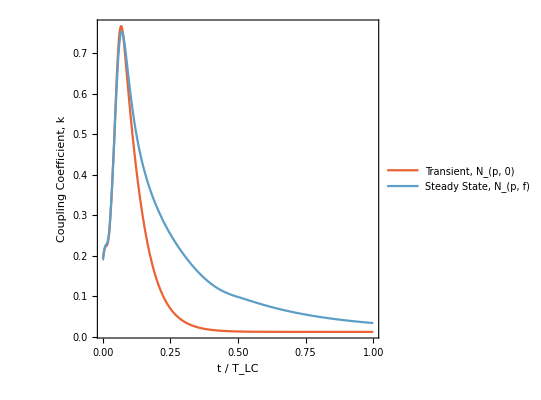

General::munfl: Exp[-990148.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.14468×10^6] is too small to represent as a normalized machine number; precision may be lost.

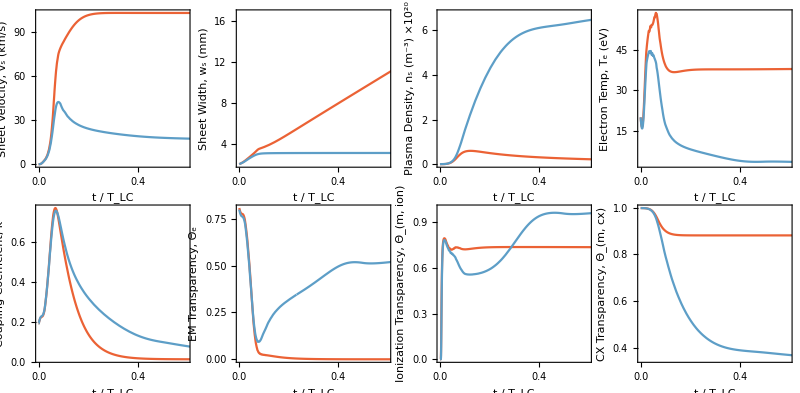

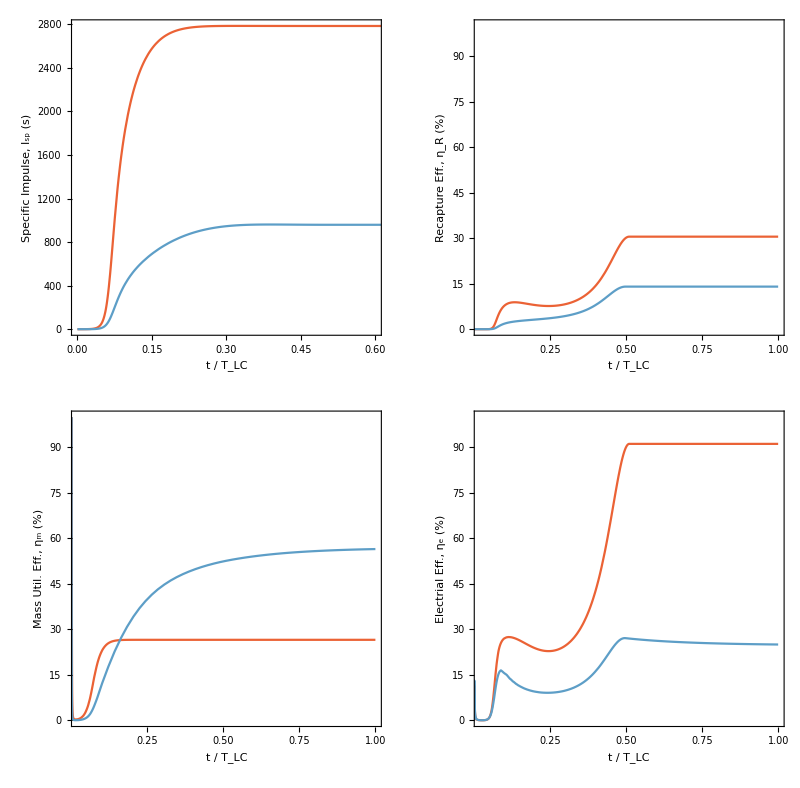

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC1]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lc1 scale,Fun2[Τ τLC1]/Lc1 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Axislabel_]:=Plot[{Fun1[Τ τLC1]100,Fun2[Τ τLC1]100},{Τ,0,1},
PlotRange->{{0.02,1.0},{0,100}},
PlotStyle->{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

(** Transparency Calculations **)
za=-0.002; 
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    

SionAr[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcxAr= 5 10^-19;
σenAr=4 10^-20;  

ΛAr[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiAr[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛAr[ne,Te]  (* e-i collision frequency *)
νenAr[nn_,Te_]:=nn σenAr ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclAr[ne_,nn_,Te_]:=(me (νeiAr[ne,Te]+νenAr[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdAr[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclAr[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δsi[t_]=δsdAr[L01+Lc1-Mi1[t]^2/Lc1,C01,nsi1[t],nni1[zsi1[t],t]+nfi1[t],Tei1[t]];
δsf[t_]=δsdAr[L01+Lc1-Mf1[t]^2/Lc1,C01,nsf1[t],nnf1[zsf1[t],t]+nff1[t],Tef1[t]];

Θsi[t_]=Exp[-3wsi1[t]/δsi[t]];
Θsf[t_]=Exp[-3wsf1[t]/δsf[t]];

Θmioni[t_]=Exp[(-nsi1[t]wsi1[t]SionAr[Tei1[t]])/vsi1[t]];
Θmionf[t_]=Exp[(-nsf1[t]wsf1[t]SionAr[Tef1[t]])/vsf1[t]];

Θmcexi[t_]=Exp[-nsi1[t] wsi1[t]σcxAr];
Θmcexf[t_]=Exp[-nsf1[t] wsf1[t]σcxAr];

(** Legend Generator **)
Plot[{Mi1[Τ τLC1]/Lc1,Mf1[Τ τLC1]/Lc1},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[7]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"Transient, N_(p, 0)", "Steady State, N_(p, f)"},
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Thesis Output **)
Print[GraphicsGrid[{
{JPlot[vsi1,vsf1,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[wsi1,wsf1,"Sheet Width, w_s (mm)",10^3],JPlot[nsi1,nsf1,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Tei1,Tef1,"Electron Temp, T_e (eV)",1]},
{JkPlot[Mi1,Mf1,"Coupling Coefficient, k",1],JPlot[Θsi,Θsf,"EM Transparency, Θ_e",1],JPlot[Θmioni,Θmionf,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcexi,Θmcexf,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];

Print[GraphicsGrid[{
{JPlot[Ispi1,Ispf1,"Specific Impulse, I_sp (s)",1],EffJPlot[ηTreci1,ηTrecf1,"Recapture Eff., η_R (%)"]},
{EffJPlot[ηmi1,ηmf1,"Mass Util. Eff., η_m (%)"],EffJPlot[EnergyFraci1,EnergyFrac1,"Electrial Eff., η_e (%)"]}},
Spacings->{5,-5}, ImageSize-> 800]];
```

## Thesis Formatting, Propellant Comparison, Rev 1

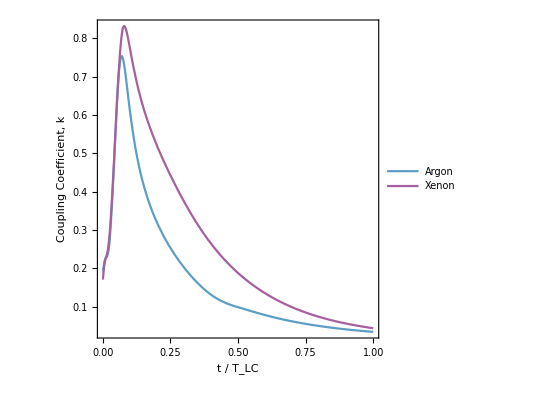

General::munfl: Exp[-1.14468×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.71742×10^6] is too small to represent as a normalized machine number; precision may be lost.

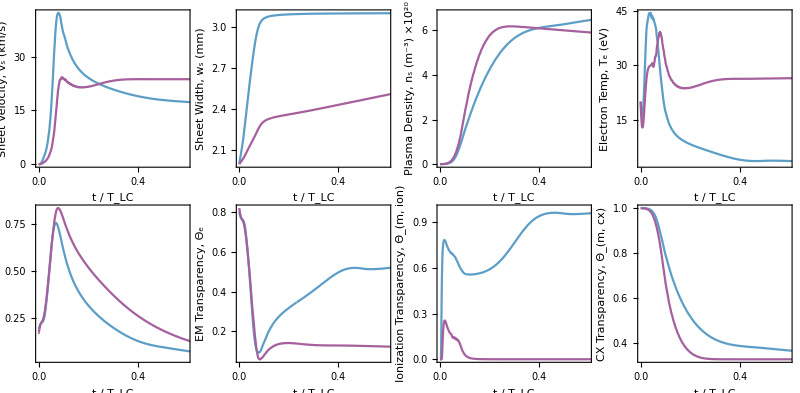

```mathematica
(** Adjust plot styles **)
JPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
JkPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]/Lc1 scale,Fun2[Τ τLC2]/Lc2 scale},{Τ,0,1},
PlotRange->{{0,0.6},All},
PlotStyle->{ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];
EffJPlot[Fun1_,Fun2_,Axislabel_,scale_]:=Plot[{Fun1[Τ τLC1]scale,Fun2[Τ τLC2]scale},{Τ,0,1},
PlotRange->{{0.02,0.6},{0,1}},
PlotStyle->{ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC",Axislabel},
Axes->False,
LabelStyle->{12,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}];

τLC1=N[2π(C01 Lc1)^(1/2)];
τLC2=N[2π(C02 Lc2)^(1/2)];

(** Transparency Calculations **)
za=-0.002; 
ec=1.6 10^-19;   
me=9.11 10^-31; 
kb=1.38 10^-23;  
g0=9.81; 
γ=5/3;  
μ0=4π 10^-7; 
ϵ0=8.85 10^-12;    

SionAr[Te_]:= 2.34 10^-14 Te^0.59 Exp[-17.44/Te]; (* Argon *)
σcxAr= 5 10^-19;
σenAr=4 10^-20;  
SionXe[Te_]:= 10^-20 (-0.0001031 Te^2+6.386 Exp[-12.127/Te])(8ec Te/(π me))^(1/2); (* Xenon *)
σcxXe= 7.5 10^-19;
σenXe=5 10^-20; 

ΛAr[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiAr[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛAr[ne,Te]  (* e-i collision frequency *)
νenAr[nn_,Te_]:=nn σenAr ((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclAr[ne_,nn_,Te_]:=(me (νeiAr[ne,Te]+νenAr[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdAr[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclAr[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)
ΛXe[ne_,Te_]:=Piecewise[{{23-Log[(ne 10^-6)^(1/2)Te^(-3/2)],Te<7.389},{24-Log[(ne 10^-6)^(1/2)Te^-1],Te≥7.389}}]    (* Coulomb Logarithm *)
νeiXe[ne_,Te_]:=2.91 10^-12 ne Te^(-3/2)ΛXe[ne,Te]  (* e-i collision frequency *)
νenXe[nn_,Te_]:=nn σenXe((8 ec Te)/(π me))^(1/2)    (*e-n collision frequency *)
ηclXe[ne_,nn_,Te_]:=(me (νeiXe[ne,Te]+νenXe[nn,Te]))/(ne ec^2)   (* Plasma Resistivity - Classical *)
δsdXe[Lterm_,Cp_,ne_,nn_,Te_]:=((2(ηclXe[ne,nn,Te])(Lterm Cp)^(1/2))/μ0)^(1/2)   (* Skin Depth *)

δs1[t_]=δsdAr[L01+Lc1-Mf1[t]^2/Lc1,C01,nsf1[t],nnf1[zsf1[t],t]+nff1[t],Tef1[t]];
δs2[t_]=δsdXe[L02+Lc2-Mf2[t]^2/Lc2,C02,nsf2[t],nnf2[zsf2[t],t]+nff2[t],Tef2[t]];

Θs1[t_]=Exp[-3wsf1[t]/δs1[t]];
Θs2[t_]=Exp[-3wsf2[t]/δs2[t]];

Θmion1[t_]=Exp[(-nsf1[t]wsf1[t]SionAr[Tef1[t]])/vsf1[t]];
Θmion2[t_]=Exp[(-nsf2[t]wsf2[t]SionXe[Tef2[t]])/vsf2[t]];

Θmcex1[t_]=Exp[-nsf1[t] wsf1[t]σcxAr];
Θmcex2[t_]=Exp[-nsf2[t] wsf2[t]σcxXe];

(** Legend Generator **)
Plot[{Mf1[Τ τLC1]/Lc1,Mf2[Τ τLC2]/Lc2},{Τ,0,1},
PlotRange->{{0,1},All},
PlotStyle->{ColorData[97,"ColorList"][[7]],ColorData[97,"ColorList"][[9]]},
Frame->True,
AspectRatio->1,
FrameLabel->{"t / Τ_LC","Coupling Coefficient, k"},
PlotLegends->{"Argon", "Xenon"},
Axes->False,
LabelStyle->{18,Black,FontFamily->"Times"},
FrameStyle->Thickness[0.004],
FrameTicksStyle->Black,
BaseStyle->{FontFamily->"Times"}]

(** Thesis Output **)
Print[GraphicsGrid[{
{JPlot[vsf1,vsf2,"Sheet Velocity, v_s (km/s)",10^-3],JPlot[wsf1,wsf2,"Sheet Width, w_s (mm)",10^3],JPlot[nsf1,nsf2,"Plasma Density, n_s (m^-3) ×10^20",10^-20],JPlot[Tef1,Tef2,"Electron Temp, T_e (eV)",1]},
{JkPlot[Mf1,Mf2,"Coupling Coefficient, k",1],JPlot[Θs1,Θs2,"EM Transparency, Θ_e",1],JPlot[Θmion1,Θmion2,"Ionization Transparency, Θ_(m, ion)",1],JPlot[Θmcex1,Θmcex2,"CX Transparency, Θ_(m, cx)",1]}},
Spacings->{5,-5}, ImageSize-> 800]];
```